```mathematica
qq[k_]:=(√((k-1) (k-2)))/(2+√((k-1) (k-2)))
```

```mathematica
l[q_,k_]:=((k-1) q +√((k-1)^2 q^2+k(k-1)(k-2)(1-q)^2))/(2k)
```

```mathematica
F[k_,q_,x_]:=(x*Log[x/(q-x)])/(k-2+(x(q-2 x))/((k-1)((1-q)/2)^2+x(q-x)))
```

```mathematica
l3[q_]:=If[q≤qq[3],l[q,3],q]
```

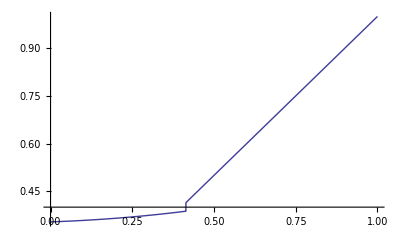

```mathematica
Plot[l3[q],{q,0,1}]
```

```mathematica
Plot3D[F[3,l[q,3],x],{x,0,1},{q,0,1},AxesLabel->{x,q,F}]
```

-Graphics3D-

```mathematica
Plot3D[F[3,l3[q],x],{q,0,1},{x,0,1},AxesLabel->{q,x,F}]
```

-Graphics3D-

```mathematica
x0=Table[l3[0.01 i]/2,{i,1,100}];
```

```mathematica
r=x/.Table[FindRoot[F[3,l3[0.01 i],x]==0.01 j,{x,x0[[i]]}],{i,1,100},{j,1,100}];
```

```mathematica
ListPlot3D[r,AxesLabel->{"q","r","x"}]
```

-Graphics3D-

```mathematica
Ps[α_,β_,γ_,δ_,k_]:=Binomial[k-2,α]/Binomial[α+β+γ+δ,k](β γ +(α-k+2)/(k-1) δ)
```

```mathematica
P[α_,β_,γ_,δ_,k_]:=α^(k-2)k(k-1) (β γ+(α δ)/(k-1))
```

```mathematica
rr=Table[N[P[r[[i,j]] ,(1-l3[0.01 i])/2,(1-l3[0.01 i])/2,0.01 i- r[[i,j]],3]],{j,1,100},{i,1,100}];
```

```mathematica
ListPlot3D[rr]
```

-Graphics3D-

```mathematica
sol=y/.Table[FindRoot[y Log[P[r[[i,j]],(1-l3[0.01 i])/2,(1-l3[0.01 i])/2,l3[0.01 i]-r[[i,j]],3]]-r[[i,j]] Log[r[[i,j]]]-(l3[0.01 i]-r[[i,j]]) Log[(l3[0.01 i]-r[[i,j]])]-(1-l3[0.01 i])Log[(1-l3[0.01 i])/2]==0,{y,0.01 j}],{i,1,99},{j,1,100}];
```

```mathematica
ListPlot3D[sol,AxesLabel->{"x","q","r"}]
```

-Graphics3D-

```mathematica
r1=Table[sol[[1,j]],{j,1,100}];
```

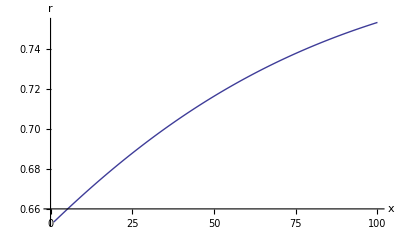

```mathematica
ListLinePlot[r1,AxesLabel->{"x","r"}]
```

```mathematica
r2=Table[sol[[i,1]], 0.01i,{i,1,99}];
```

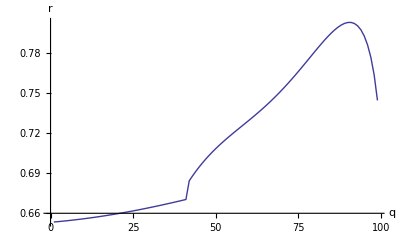

```mathematica
ListLinePlot[r2,AxesLabel->{"q","r"}]
```

```mathematica
r3=Table[sol[[i,50]],{i,1,99}];
```

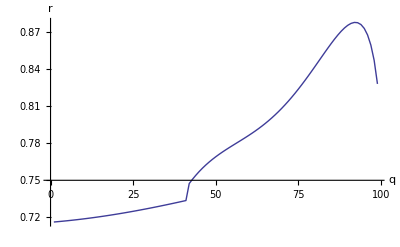

```mathematica
ListLinePlot[r3,AxesLabel->{"q","r"}]
```